# Complex Integration

### Cauchy and Morera Theorems

Theorem 4.2 p96:  f(z) analytic and singularity free on and within a closed contour Γ implies ∮_Γ f(z)dz=0.

Theorem 4.3 p97: f continuous on a domain and ∮_Γ f(z)dz=0 for any closed contour within the domain implies f is analytic on the domain.

Proofs on the board!

Calculus III Reminder:
https://en.wikipedia.org/wiki/Green%27s_theorem
Check we match Wiki
https://en.wikipedia.org/wiki/Cauchy%27s_integral_theorem
https://en.wikipedia.org/wiki/Morera%27s_theorem

### Deforming Contours

As long as we do not cross any singularities we can make closed contours round isolated singularities much simpler.

Illustration on the board!

Simple contours are “tiny circles” round singularities joined by paired “two-way” contours!

### Simple Contours

Integrals on “tiny circles” around singularities can be computed analytically.
Paired “two-way” contour integrals cancel.

### Integration for Poles on Tiny Circles.

A counter clockwise parametrization for a tiny circle around a pole f[z]=r/(z-c)^n is z(t)=c+ϵ E^(2π ⅈ t) with z'[t]=2π ⅈ ϵ E^(2π ⅈ t).

#### For n=1 “a simple pole”

∫_0^1 f[z[t]]*z'[t]dt=∫_0^1 r/(z[t]-c)*z'[t]dt=∫_0^1 r/(c+ϵ E^(2π ⅈ t)-c)*2π ⅈ ϵ E^(2π ⅈ t)dt
=∫_0^1 r/(ϵ E^(2π ⅈ t))*2π ⅈ ϵ E^(2π ⅈ t)dt=∫_0^1 r/ϵ*2π ⅈ ϵ dt=∫_0^1 r*2π ⅈ dt=2π ⅈ r

The counter clockwise integral around a simple pole r/(z-c) is 2 π  ⅈ r.

#### For n=2 “a double pole”

(∫_0^1 f[z[t]]*z'[t]dt=∫_0^1 r/(z[t]-c)^2*z'[t]dt=∫_0^1 r/((ϵ E^(2π ⅈ t))^2)*2π ⅈ ϵ E^(2π ⅈ t)dt=∫_0^1 r/(ϵ^2 E^(4π ⅈ t))*2π ⅈ ϵ E^(2π ⅈ t)dt
=(2π ⅈ)/ϵ∫_0^1 E^(2π ⅈ t)dt=(2π ⅈ)/ϵ E^(2π ⅈ t)/(2π ⅈ)])_(t=0)^1=0

The counter clockwise integral around a double pole r/(z-c)^2 is 0.

#### For n≠1 “any pole except a simple pole”

(∫_0^1 f[z[t]]*z'[t]dt=∫_0^1 r/((ϵ E^(2π ⅈ t))^n)*2π ⅈ ϵ E^(2π ⅈ t)dt=(2π ⅈ)/ϵ^(n-1)∫_0^1 E^(2(n-1)π ⅈ t)dt=(2π ⅈ)/ϵ E^(2π ⅈ t)/(2π (n-1) ⅈ)])_(t=0)^2=0

The counter clockwise integral around any non-simple pole  r/(z-c)^n i.e. n≠1 is 0.

### Winding Number

The winding number of w(c) for a contour Γ around a point c is the number of times the contour winds around the contour in the counter clockwise direction.  Negative winding numbers indicate clockwise winding.  The winding number of a singularity gives the number of circum-navigations when we shrink contours down to “tiny-circles”.

### Residue Theorem

If a contour Γ encloses an analytic function f(z) with a finite number simple poles c_1,c_2,…,c_m then 
	∫_Γ f(z)dz=2π ⅈ   ∑_(j=1)^m w(c_j) r_j
where the residues r_j=lim_(z→c_j) (z-c_j)f(z) gives the behavior f(z)∼r_j/(z-c_j) for z≈c_j.  
https://en.wikipedia.org/wiki/Residue_theorem

### Practice Example 1

a) Setup Calculus 2 integrals for ∫_Γ f(z)dz where Γ is the edge of the axis aligned square with corners at -2 and 2+2ⅈ.

b) Compute∫_Γ f(z)dz for f(z)=z^2 using part a.

c) Explain how to compute∫_Γ f(z)dz for f(z)=z^2 the easy way.

c) Explain how to compute∫_Γ f(z)dz for f(z)=z^2+(3ⅈ)/(z-ⅈ)+2/(z+ⅈ) the easy way.

### Practice Example 2

a) Setup Calculus 2 integrals for ∫_Γ f(z)dz where Γ is the chunk of the real axis from -2<x<2  closed with the top half semicircle of radius 2.

b) Compute∫_Γ f(z)dz for f(z)=z^2 using part a.

c) Explain how to compute∫_Γ f(z)dz for f(z)=z^2 the easy way.

c) Explain how to compute∫_Γ f(z)dz for f(z)=z^2+(3ⅈ)/(z-ⅈ)+2/(z+ⅈ) the easy way.

### Practice Example 3

Compute ∫_(-∞)^∞ 1/(x^2+4)dx.  Explain all your steps.

### Practice Example 4

Compute ∫_(-∞)^∞ x/((x^2+4)(x^2+2x+2))dx.  Explain all your steps.

We should be able to see fairly fast where the -π/10 is coming from!

```mathematica
Integrate[x/((x^2+4)(x^2+2x +2)),{x, -∞,∞}]
```

-π/10

### Practice Example 5

Outline how to compute ∫_(-∞)^∞ (cos(x))/(x^2+4)dx.  It might help to remember that cos(z)=0.5 (ⅇ^(ⅈ z)+ⅇ^(-ⅈ z))

```mathematica
TabView[{
"ⅇ^ⅈz"->ComplexPlot3D[E^(I z),{z,2}],
"ⅇ^-ⅈz"->ComplexPlot3D[E^(-I z),{z,2}]
}]
```

12

π/(2 ⅇ^2)

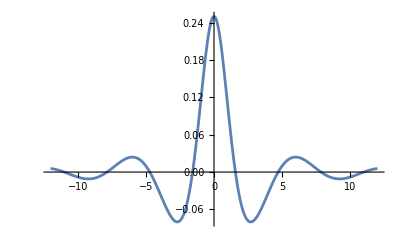

```mathematica
Integrate[Cos[x]/(x^2+4),{x,-∞,∞}]
Plot[Cos[x]/(x^2+4),{x,-12,12},PlotRange->All]
```